```mathematica
ClearAll["Global`*"]
$Assumptions={a>0,t>0,kβ>0,s>0};
```

The Magnus expansion allows the calculation of a transfer matrix for our differential equation using a series expansion in terms of commutators of the matrix initial value problem.

```mathematica
Commutator[A1_,A2_]:=A1.A2-A2.A1;
A[t_]:={{0,1},{-kβ[t]^2,0}};
Ω1[t_]:=∫_0^t A[ξ] ⅆξ;
Ω2[t_]:=-1/2 ∫_0^t ∫_0^ξ1 Commutator[A[ξ2],A[ξ1]] ⅆξ2 ⅆξ1;
Ω31[t_]:=1/12 ∫_0^t ∫_0^ξ1 ∫_0^ξ1 Commutator[A[ξ3],Commutator[A[ξ2],A[ξ1]]] ⅆξ3 ⅆξ2 ⅆξ1
Ω32[t_]:=1/4 ∫_0^t ∫_0^ξ1 ∫_0^ξ2 Commutator[Commutator[A[ξ3],A[ξ2]],A[ξ1]] ⅆξ3 ⅆξ2 ⅆξ1
Ω2[t]
Ω31[t]
Ω32[t]
```

{{-1/2 ∫_0^t ∫_0^ξ1 (-kβ[ξ1]^2+kβ[ξ2]^2)ⅆξ2ⅆξ1,0},{0,-1/2 ∫_0^t ∫_0^ξ1 (kβ[ξ1]^2-kβ[ξ2]^2)ⅆξ2ⅆξ1}}

{{0,1/12 ∫_0^t ∫_0^ξ1 ξ1 (2 kβ[ξ1]^2-2 kβ[ξ2]^2)ⅆξ2ⅆξ1},{1/12 ∫_0^t ∫_0^ξ1 ∫_0^ξ1 (2 kβ[ξ1]^2 kβ[ξ3]^2-2 kβ[ξ2]^2 kβ[ξ3]^2)ⅆξ3ⅆξ2ⅆξ1,0}}

{{0,1/4 ∫_0^t ∫_0^ξ1 ∫_0^ξ2 (-2 kβ[ξ2]^2+2 kβ[ξ3]^2)ⅆξ3ⅆξ2ⅆξ1},{1/4 ∫_0^t ∫_0^ξ1 ∫_0^ξ2 (-2 kβ[ξ1]^2 kβ[ξ2]^2+2 kβ[ξ1]^2 kβ[ξ3]^2)ⅆξ3ⅆξ2ⅆξ1,0}}

```mathematica
(*The transfer matrix is given by MatrixExp[Ω1[t]+Ω2[t]]]*)
```

The general version for the first two terms in the expansion isn’t very enlightening but if the integrals can be evaluated explicitly then it might prove useful. The first case is of course the uniform plasma density. Clearly, all the commutators go to zero so only the first term in the Magnus expansion remains.

```mathematica
kβ[t_]=k;
Ω1[t]
FullSimplify[MatrixExp[Ω1[t]]]
```

{{0,t},{-k^2 t,0}}

{{Cos[k t],Sin[k t]/k},{-k Sin[k t],Cos[k t]}}

Lets compare to a ramp with an exact solution.

```mathematica
kβ[t_]=1/(1+a t);
Ω1[t]
Ω2[t]
sol1=FullSimplify[MatrixExp[Ω1[t]]];
sol2=FullSimplify[MatrixExp[Ω1[t]+Ω2[t]]];
sol3=FullSimplify[MatrixExp[Ω1[t]+Ω2[t]+Ω31[t]+Ω32[t]]];
```

{{0,t},{-t/(1+a t),0}}

{{-((a t (2+a t))/(1+a t)-2 Log[1+a t])/(2 a^2),0},{0,((a t (2+a t))/(1+a t)-2 Log[1+a t])/(2 a^2)}}

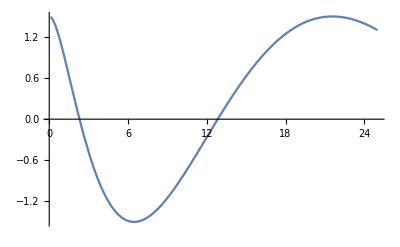

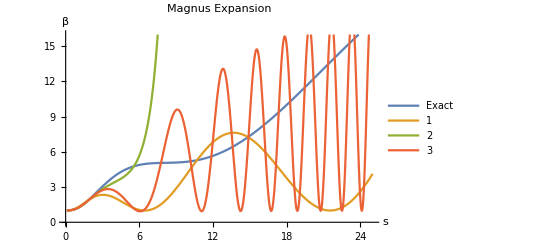

```mathematica
x0={1.5,0};
rep={t->s,a->.5};
x1[s_]:=(sol1.x0)/.rep;
x2[s_]:=(sol1.x0)/.rep;
x3[s_]:=(sol1.x0)/.rep;
β0=1.;
α0=-.01;
γ0=(1+α0^2)/β0;
αm0=-a/2;
c1=((α0-αm0 β0)^2+1)/(2 β0 (αm0^2-1))+β0/2;
c2=(α0-αm0 β0)/(√(1-αm0^2));
c0=√(c1^2+c2^2+1/(1-αm0^2));
Φ[s_]:=1/(2 αm0) √(1-αm0^2) Log[1/kβ[s]];
βa[s_]:=(1/kβ[s] (c0+c1 Cos[2 Φ[s]]+c2 Sin[2 Φ[s]]))/.rep;
β1[s_]:=(sol1[[1, 1]]^2 β0-2 sol1[[1,1]] sol1[[1,2]] α0+sol1[[1,2]]^2 γ0)/.rep;
β2[s_]:=(sol2[[1, 1]]^2 β0-2 sol2[[1,1]] sol2[[1,2]] α0+sol2[[1,2]]^2 γ0)/.rep;
β3[s_]:=(sol3[[1, 1]]^2 β0-2 sol3[[1,1]] sol3[[1,2]] α0+sol3[[1,2]]^2 γ0)/.rep;
Plot[x1[s][[1]],{s,0.1,25}]
Plot[{βa[s],β1[s],β2[s],β3[s]},{s,0.1,25},PlotRange->{{0, 25},{0, 16}},
AxesLabel->{"s", "β"},PlotLabel->"Magnus Expansion",PlotLegends->{"Exact","1","2","3"}]
```

The lowest order of the Magnus expansion can be calculated exactly.

```mathematica
Clear[kβ,β0,α0,γ0]
FullSimplify[MatrixExp[Ω1[t]],kβ>0]
```

{{Cosh[√(t ∫_0^t -kβ[ξ]^2ⅆξ)],(t Sinh[√(t ∫_0^t -kβ[ξ]^2ⅆξ)])/(√(t ∫_0^t -kβ[ξ]^2ⅆξ))},{√((∫_0^t -kβ[ξ]^2ⅆξ)/t) Sinh[√(t ∫_0^t -kβ[ξ]^2ⅆξ)],Cosh[√(t ∫_0^t -kβ[ξ]^2ⅆξ)]}}

```mathematica
M={{Cos[√(s I0)],√(s/I0) Sin[√(s I0)]},{-√(I0/s) Sin[√(s I0)],Cos[√(s I0)]}};
FullSimplify[β0 M[[1,1]]^2-2 α0 M[[1,1]] M[[1,2]]+γ0 M[[1,2]]^2]
```

β0 Cos[√(I0 s)]^2+(s γ0 Sin[√(I0 s)]^2)/I0-√(s/I0) α0 Sin[2 √(I0 s)]

```mathematica
TrigReduce[β0 Cos[√(I0 s)]^2+(s γ0 Sin[√(I0 s)]^2)/I0-√(s/I0) α0 Sin[2 √(I0 s)]]
```

(I0 β0+s γ0+I0 β0 Cos[2 √(I0 s)]-s γ0 Cos[2 √(I0 s)]-2 I0 √(s/I0) α0 Sin[2 √(I0 s)])/(2 I0)

#### Up to second order analytically

The first and second term in the expansion can be included and produce a reasonably simple analytic solution. The only complicated part is the integral in the second term.

```mathematica
kβ[s_]:=Piecewise[{{√(1-a s),s<1/a},{0,s≥1/a}}];
Ω1[s]
Ω2[s]
Ω31[s]+Ω32[s]
det[s_]=Det[Ω1[s]+Ω2[s]];
```

{{0,s},{Piecewise[{{-1/(2 a), a>0&&1/a-s<0}, {1/2 (-2 s+a s^2), True}}],0}}

{{-1/2 (Piecewise[{{(a s^3)/6, 1/a-s≥0||a≤0}, {(-2+3 a s)/(6 a^2), True}}]),0},{0,-1/2 (Piecewise[{{-(a s^3)/6, 1/a-s≥0||a≤0}, {(2-3 a s)/(6 a^2), True}}])}}

{{0,1/12 (Piecewise[{{-(a s^4)/4, 1/a-s≥0||a≤0}, {(1-2 a^2 s^2)/(4 a^3), True}}])+1/4 (Piecewise[{{(a s^4)/12, 1/a-s≥0||a≤0}, {(3-8 a s+6 a^2 s^2)/(12 a^3), True}}])},{1/4 (Piecewise[{{1/(60 a^3), a>0&&1/a-s<0}, {-1/60 a s^4 (-5+4 a s), True}}])+1/12 (Piecewise[{{(7-10 a s)/(20 a^3), a>0&&1/a-s<0}, {1/20 a s^4 (-5+2 a s), True}}]),0}}

```mathematica
det1[s_]=Det[Ω1[s]];
det2[s_]=Det[Ω1[s]+Ω2[s]];
det3[s_]=Det[Ω1[s]+Ω2[s]+Ω31[s]+Ω32[s]];
```

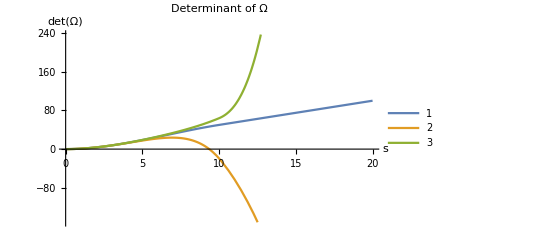

```mathematica
Plot[{det1[s]/.{a->0.1},det2[s]/.{a->0.1},det3[s]/.{a->0.1}},{s,0.0,20},AxesLabel->{"s", "det(Ω)"},PlotLabel->"Determinant of Ω",PlotLegends->{"1","2","3"}]
```